## Numbers

```mathematica
ℏ=1.05457*10^-34;
λ=852.0*10^-9;
ks=(2π)/λ; (*wavevector for the short lattice*)
kl=π/λ; (*wavevector for the long lattice*)
a=λ/2;  (*short lattice spacing*)
amu=1.6605*10^-27;
mRb=86.909*amu;  (*mass or Rb87*)
Er=(ℏ^2 ks^2)/(2mRb); (*Recoil energy of the short lattice*)
as=5.3*10^-9;   (*approximate s-wave scattering length for Rb87 (in meters)*)
```

```mathematica
Er/(2π*ℏ)
```

3162.59

```mathematica
ℏ^2/(mRb*waist^2*2*π*ℏ)
```

206.761

```mathematica
mRb
```

1.44312×10^-25

## Comparing Sinusoidal Potential Tunneling and Onsite to 2 Gaussian Wells:

```mathematica
(*The tunneling rate due to a sinusoid potential is given by the difference between the ground state, and the next excited state. The excited states are given by  the mathieu characterisc functions- which essentially exactly solve the schrodinger equation for a cos potential*)
```

```mathematica
(*For our interest, we will work with Vkauf, which corresponds to having 100*recoilenergy depth lattice.
```

```mathematica
L =900*10^-9(*Use Adam's interwell seperation*)
```

9/10000000

```mathematica
Vkauf*scalin
```

316259.

```mathematica
Et = ℏ^2*2*π^2/(mRb*L^2);Et2 = π^2*ℏ^2/(2*mRb*(L/2)^2);
```

```mathematica
Jx=(1/2*MathieuCharacteristicA[1,(Vkauf*scalin*(2*π*ℏ)*1/(Et*2))]-1/2* MathieuCharacteristicA[0,Vkauf*scalin*(2*π*ℏ)*1/(Et*2)])*Et/(2*π*ℏ)
```

47645.2

-78468.5

```mathematica
1/4* MathieuCharacteristicA[0,Vkauf*scalin*(2*π*ℏ)*1/(Et*2)]
```

-17.1416

```mathematica
Vkauf*scalin*1/(Et*2)
```

6.11542×10^34

```mathematica
(*I am not sure about this, so I will double check this with numerics*)
```

#### NUMERICS FOR SINUSOID:

```mathematica
(*First, find the matrix elements*)
```

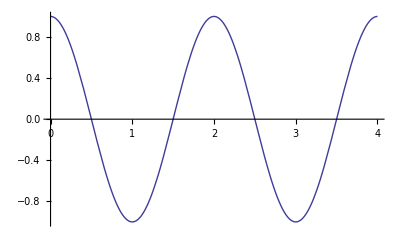

```mathematica
Plot[Cos[((2*π*x)/2)],{x,0,4}]
```

```mathematica
HSin[V_,p_] := Table[m^2*KroneckerDelta[m,l]+V*.5*(KroneckerDelta[m,l+2]+KroneckerDelta[m,l-2]),{m,-p/2,p/2},{l,-p/2,p/2}]//Chop
```

```mathematica
Mod[8
```

```mathematica
HSin[10,10]//MatrixForm
```

(25. | 0 | 5. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16. | 0 | 5. | 0 | 0 | 0 | 0 | 0 | 0 | 0
5. | 0 | 9. | 0 | 5. | 0 | 0 | 0 | 0 | 0 | 0
0 | 5. | 0 | 4. | 0 | 5. | 0 | 0 | 0 | 0 | 0
0 | 0 | 5. | 0 | 1. | 0 | 5. | 0 | 0 | 0 | 0
0 | 0 | 0 | 5. | 0 | 0 | 0 | 5. | 0 | 0 | 0
0 | 0 | 0 | 0 | 5. | 0 | 1. | 0 | 5. | 0 | 0
0 | 0 | 0 | 0 | 0 | 5. | 0 | 4. | 0 | 5. | 0
0 | 0 | 0 | 0 | 0 | 0 | 5. | 0 | 9. | 0 | 5.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5. | 0 | 16. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5. | 0 | 25.)

```mathematica
|
```

```mathematica
Eigenvalues[HSin[(100*Er*1/Et2),200]-1000000*IdentityMatrix[201],3]+1000000
```

{-68.5662,-68.5662,-44.1478}

```mathematica
200^2
```

40000

```mathematica
(100*Er*1/Et2)
```

81.0423

```mathematica
o=Eigensystem[HSin[(100*Er*1/Et2),3]-100000*IdentityMatrix[4]];
```

```mathematica
MathieuCharacteristicA[1,(100*Er*1/(Et2*2))]
```

-44.1478

```mathematica
MathieuCharacteristicB[1,(100*Er*1/(Et2*2))]
```

-68.5662

```mathematica
o[[2]][[1]]//Chop
```

{-0.493783,-0.506141,0.506119,0.493804}

```mathematica
o[[2]][[2]]//Chop
```

{0.493804,-0.506119,-0.506141,0.493783}

```mathematica
o[[1]]
```

{-100039.,-100039.,-99958.2,-99958.2}

```mathematica
(*I am satisfied, apart from the degeneracy, which I don't quite understand: tunneling is given by = (Math1-Math0)/2*)
(*Why don't we plot the tunneling rate as a function of the plot depth*)
```

```mathematica
tunel[V_]:=1/2(MathieuCharacteristicA[.999,(V*Er*1/(Et2*2))]-MathieuCharacteristicA[0,(V*Er*1/(Et2*2))])
```

```mathematica
tunplotvsV = Table[{V,tunel[V]*Et2/(2*π*ℏ)},{V,0,200,1}]
```

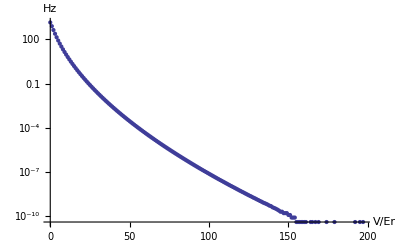

```mathematica
p1 = ListLogPlot[tunplotvsV,AxesLabel->{"V/Er","Hz"}]
```

```mathematica
(*This compared with the tunneling rates at around 34 Hz that we were predicting in the gaussian well*)
```

```mathematica
MathieuCharacteristicA[1,(200*Er*1/(Et2*2))]-MathieuCharacteristicA[0,(200*Er*1/(Et2*2))]
```

34.9794

```mathematica
Et2
```

```mathematica
(2.585748047643158*^-30)/(2*π*ℏ)
```

3902.39

```mathematica
Er/Et2
```

0.810423

```mathematica
TunNum[V_]:= Module[{tune,Eig},
Eig = Eigenvalues[HSin[(V*Er*1/Et2),200]-1000000*IdentityMatrix[201],2];
tune= Eig[[2]]-Eig[[1]]
]
```

```mathematica
TunNum[10]
```

0.0204735

```mathematica
tunnumlist = Table[{V,TunNum[V]},{V,0,200}];
```

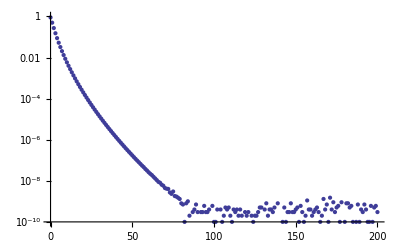

```mathematica
ListLogPlot[{tunnumlist/.{ {x_,y_}->{x,y*Et2/Er}}}]
```

```mathematica
-
```

```mathematica
tunnumlistZOL = Table[{V,TunNum[V]},{V,5,25}];
```

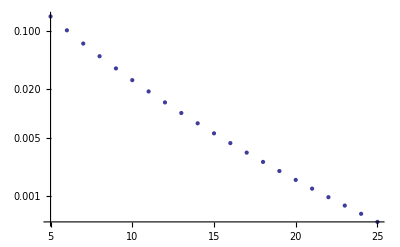

```mathematica
ListLogPlot[{tunnumlistZOL/.{ {x_,y_}->{x,y*Et2/Er}}}]
```

```mathematica
(*Matches up! Nice*)
```

```mathematica
tunnumlistZOL = Table[{V,TunNum[V]},{V,0,25}];
```

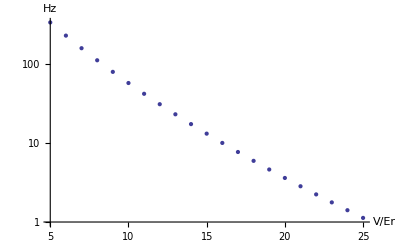

```mathematica
ListLogPlot[{tunnumlistZOL/.{ {x_,y_}->{x,y*Et2/(2*π*ℏ)}}},AxesLabel->{"V/Er","Hz"}]
```

## Functions:

```mathematica
Clear[h]
Clear[M]
h = 1.05457173*10^-34;
M = 1.443161*10^-25;
```

```mathematica
Ψ[n_,x_,m_,y_,L_]:= 1/L*Exp[-ⅈ*2 π/L(n*x+y*m)]
```

```mathematica
Hp[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
H2p[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x+b)^2+y^2))/c^2]Φ[n,x,m,y,L]-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
HPlane[V_,L_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[(-(2*π/L)^2(n-l)^2)/8]*π*1/(2*L^2)Exp[(-(2*π/L)^2(m-q)^2)/8]
```

```mathematica
HPlanebtest[V_,L_,n_,m_,l_,q_,b_]:= 
(*I had some trouble getting the factors in EXp right, but this configuration worked. This is for one well only! This is the generalizating of HPlane, which doesn't worry about b. This basically lets me offset my one well wherever I want to double check that I have the right form of the analytics*)KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ(2*π/L)(m-q))^2/8]
```

```mathematica
H2Plane[V_,L_,b_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]-V*Exp[((-2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]//N
```

```mathematica
HMatrix[V_,L_,size_]:=ArrayFlatten[Table[HPlane[V,L,m,l,n,q],{m,-size,size},{n,-size,size},{l,-size,size},{q,-size,size}]//N]
```

```mathematica
groundState[EM_,L_,x_,y_]:=Compile[{Size=Sqrt[Length[EM]], i,j},
(*Given an eigenvector, this will compute a plottable version of the wavefunction. However, there is little sophistication, the user must still change the index conversion number by hand.

Note: there was a problem: use ky for calculating the number on x and y, as the kx function gives the row of a matrix, but, for the eigenvector, it is just a 'column' vector, so just use ky*) Sum[Normalize[EM][[(i-1)*Size+j]]*N[Exp[-ⅈ*2.*π/L*(ky[i,Size]*x+ky[j,Size]*y)]/L,8],{i,1,Size},{j,1,Size}]]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix//N]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

Harmonic Oscillator Functions:
HMV1[1,2,.1,0,.5]

```mathematica
HMV1[1,1,.1,0,0.5]
```

HMV1[1,1,0.1,0,0.5]

```mathematica
HMV1[1,2,0.1,0.5]
```

HMV1[1,2,0.1,0.5]

```mathematica
HMV1[l_,m_,ω_,b_,c_]:= (Sqrt[ω]/Sqrt[2^(l+m)Factorial[l]*Factorial[m]]*Sum[{2^k Factorial[k]*Binomial[l,k]*Binomial[m,k]*(1-2*(ω*c^2)/(1+2 c^2 ω))^((m+l)/2-k)*HermiteH[(m+l-2*k),Sqrt[ω/(1+2*c^2*ω)]*b]},{k,0,Min[m,l]}]*Exp[b^2/(2 c^2)(1/(1+2 c^2*ω)-1)]*Sqrt[2/(1+2 c^2*ω)]c)[[1]]
```

```mathematica
Hx2Anal2[l_,m_]:= 1/2(2*l+1)*KroneckerDelta[l,m]-1/2 Sqrt[(l+1)(l+2)]KroneckerDelta[l+1,m-1]-1/2 Sqrt[(m+1)(m+2)]KroneckerDelta[l-1,m+1]
```

```mathematica
HOBasis[V_,b_,c_,size_]:= Module[{ω=Sqrt[(2V)/c^2]},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,b,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{l,0,size-1},{m,0,size-1},{q,0,size-1}]]
```

```mathematica
HOBasis1Well[V_,c_,size_]:= Module[{ω=Sqrt[2*V/c^2]},Table[ω/2*Hx2Anal2[n,m]*KroneckerDelta[l,q]+ω/2*Hx2Anal2[l,q]*KroneckerDelta[m,n]-V*HMV1[n,m,ω,0,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{m,0,size-1},{l,0,size-1},{q,0,size-1}]]
```

```mathematica
plotGround[Ψ_,H_,V_,c_,b_,size_,]:= Compile[{x,k,Em,M,HOBasis},

Plot[{Sum[k,{k,Table[Ψ[n,x,V,c]*Normalize[Em[[2]][[1]]][[n+1]], {n,0,size}]}],-V/(c*Sqrt[2π])Exp[-x^2/(4.*V*c^2)]//N},{x,-10,10}]
]
```

```mathematica
plotGround
```

plotGround

```mathematica
plotGround2wellHO2d[Ψ_,V_,b_,c_,size_]:= Module[{k,ω=Sqrt[2*V/(6b*c+9 c^2)],HOBasis,Em},
HOBasis[V,b,c,size,ω]:= Module[{},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,-b,c]*HMV1[l,q,ω,b,c],{n,0,size},{l,0,size},{m,0,size},{q,0,size}]];
Em = Eigensystem[ArrayFlatten[HOBasis[1.5^2,1,.5,7,ω]-1000*IdentityMatrix[42]]]

Plot[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,x,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,17},{j,1,17}]]^2},{x,-3,3}]
]
```

```mathematica
plotGround2wellHO2dT[Ψ_,V_,b_,c_,size_,Em_]:= Module[{k,ω=Sqrt[2*V/c^2],x,y},
Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}];

Plot3D[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}]]^2},{x,-3,3},{y,-3,3}]
]
```

```mathematica
HM2Well[V_,b_,c_,size_]:= Module[{ω=Sqrt[2*V/(6*b*c+9 c^2)]},
Table[ω/2*Hx2Anal2[n,m]-V*HMV1[n,m,ω,b,c]-V*HMV1[n,m,ω,-b,c],{n,0,size},{m,0,size}]
]
```

```mathematica
EnGround2wellHO[V_,b_,c_,size_]:=EnGround2wellHO[V,b,c,size]= Module[{Em,M},

(M=HM2Well[V,b,c,size]-1000*IdentityMatrix[size+1]);
(Em=Eigenvalues[M])
]
```

### Sparse Matrices Stuff:

```mathematica
R[deltaK_,L_]:=R[deltaK]=Exp[(-(2*π/L)^2(deltaK)^2)/8.]//N
```

```mathematica
yIndex[i_,size_] =Mod[i,size,1]
```

Mod[i,size,1]

```mathematica
(*y index will take a number from 1-n, and convert it into a quantum number for ky. This will be an integer starting from -p..p.*)
```

```mathematica
yIndex[2,4]
```

2

```mathematica
ky[i_,size_]=yIndex[i,size]-(size-1)/2-1
```

-1+(1-size)/2+Mod[i,size,1]

```mathematica
(*this will convert our index number to a range that runs over negative numbers so we can get backwards waves*)
```

```mathematica
kx[i_,size_]=xIndex[i,size]-(size-1)/2-1
```

(1-size)/2+(i-Mod[i,size,1])/size

```mathematica
kx[6,5]
```

-1

```mathematica
xIndex[i_,size_]=(i-Mod[i,size,1])/size+1
```

1+(i-Mod[i,size,1])/size

```mathematica
BuildPlaneMatrix[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
BuildPlaneMatrix2D2Well[V_,L_,p_,b_]:= Module[{MDense,MDiag,i,j,M},
(* I am choosing the wells to be on the x-axis, so the y-axis dynamics shouldn't
change. Notice, the R2W contains b information, and will be used for the kx's, while the R doesn't, and can be used for the ky's without loss of generality, because there are two wells, there is another term in our MDense*)
MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->(R2W[kx[j,p]-kx[i,p],L,b]+R2W[kx[j,p]-kx[i,p],L,-b])*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
R2W[deltaK_,L_,b_]:=R2W[deltaK,L,b]=Exp[((2.*b+ⅈ(2.*π/L)(deltaK)/2)^2-4.*b^2)/2.]//N
```

```mathematica
(*Tunneling for a 2D 2Well case*)
Tunneling2DWellListGen[basisnum_]:=
(*Need to double check that L=1 is okay for small b*)Module[{EnergyList,TunnelingList},
EnergyList= Table[{b,Eigenvalues[BuildPlaneMatrix2D2Well[10,8,basisnum,b/2.]-1000.*IdentityMatrix[basisnum^2],2]+1000},{b,.1,4,.2}];

TunnelingList= Table[{EnergyList[[p]][[1]],EnergyList[[p]][[2]][[2]]-EnergyList[[p]][[2]][[1]]},{p,1,Length[EnergyList]}]
]
```

```mathematica
10/25.
```

0.4

```mathematica
(*1D Functions for plane waves*)
```

```mathematica
computePlaneMatrix2WellH[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]

]
```

```mathematica
computePlaneMatrix2WellBox[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - 1/2(V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length+V*Exp[1/(2 c^2)(-b+ⅈ*c^2(m-l))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length)-1/2(V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length+V*Exp[(1/(2 c^2)(b+ⅈ*c^2(m-l))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length);
M = Eigensystem[Table[H[π*l/length,π*m/length],{l,1,p},{m,1,p}]-10000*IdentityMatrix[p],3]

]
```

```mathematica
ComputePlaneWaveEN[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M,EM},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag;

EM = Eigenvalues[M-10000*IdentityMatrix[p^2],3]
]
```

```mathematica
(-bsep+ⅈ*c^2(l-m))^2//Expand
```

bsep^2-2 ⅈ bsep c^2 l-c^4 l^2+2 ⅈ bsep c^2 m+2 c^4 l m-c^4 m^2

```mathematica
1/2 (k-l) (2 ⅈ bsep+(-k+l) w^2)//Expand
```

ⅈ bsep k-ⅈ bsep l-(k^2 w^2)/2+k l w^2-(l^2 w^2)/2

```mathematica
Tunneling2D[V_,L_,p_,b_]:= Module[{En0,En1, EnList,T},
EnList = Eigenvalues[BuildPlaneMatrix2D2Well[V,L,p,b/2.]-1000.*IdentityMatrix[p^2],2]+1000;
En1 = EnList[[2]];
En0  =EnList [[1]];
T = En1-En0
]
```

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-1000000*IdentityMatrix[p+1],3]

]
```

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2*c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-1000000*IdentityMatrix[p+1],3]

]
```